```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tab = Import["temp_chain_regularhmc_26-10-2026","Table"];
```

```mathematica
u = tab[[;; , 7]];
```

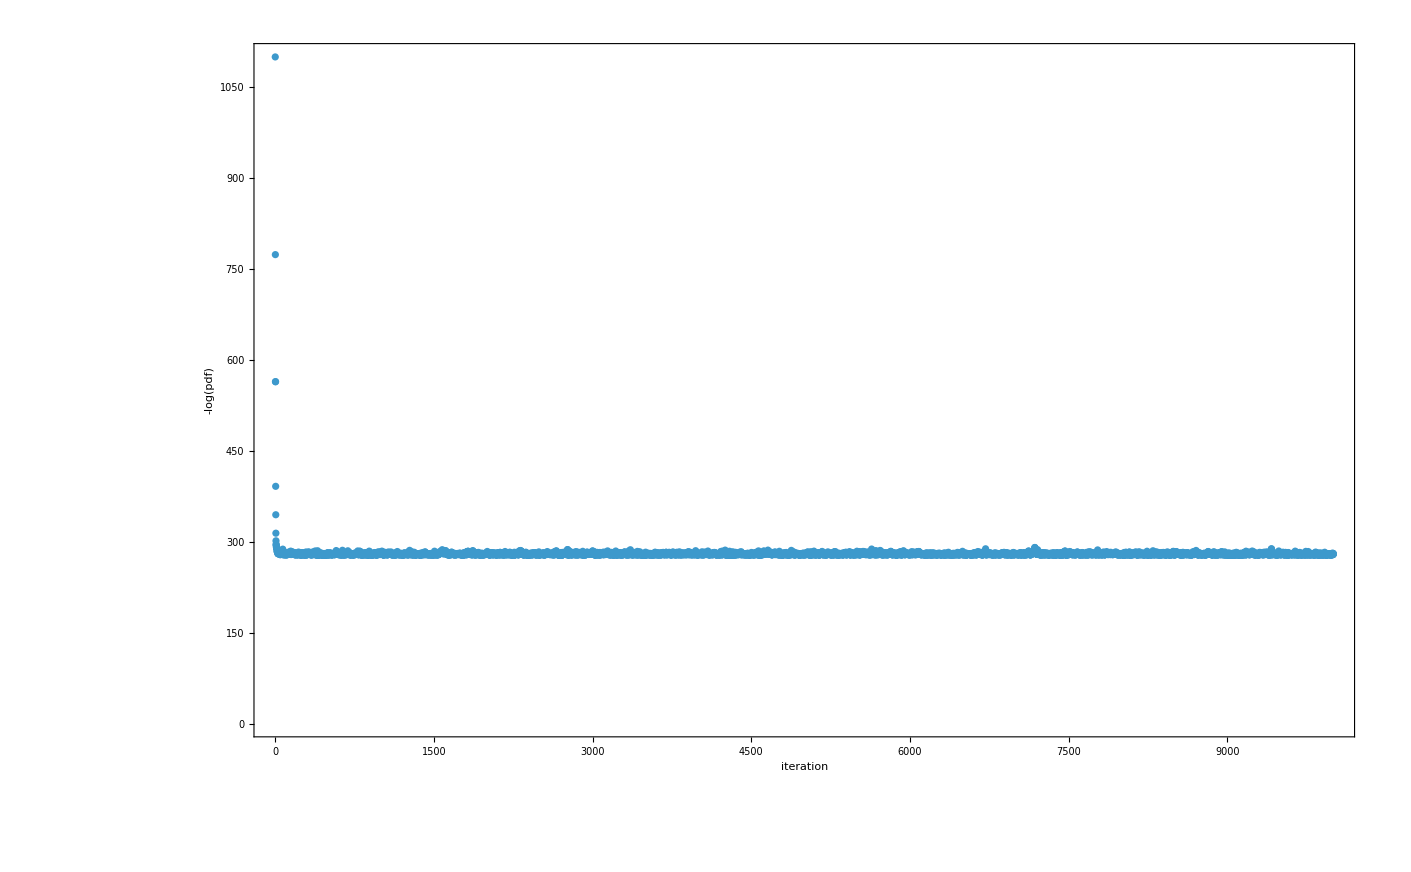

```mathematica
ListPlot[u , Axes->False , Frame->True , FrameLabel->{"iteration" , "-log(pdf)"} , PlotRange->All]
```

```mathematica
thr = 250;
```

```mathematica
chain = Table[tab[[thr;; , i]] , {i , 1 , 3}];
```

```mathematica
(*chain = Table[RandomReal[{-1000 , 1000}] , 500];*)
```

```mathematica
(*see: Geyer,Charles J.. (1992).Practical Markov Chain Monte Carlo.Statistical Science,7(4),473–483. doi:10.1214/ss/1177011137*)
```

```mathematica
ess[chain_]:= Module[{n , acf , dem},
n = Length[chain];
acf = Table[{lag , CorrelationFunction[chain , lag]} , {lag , 0 , n-1}];
dem = 1. + 2.Total[TakeWhile[(#[[1 , 2]] + #[[2,2]])&/@Partition[acf , 2] , Positive][[2;;]]];
{n / dem , acf}
]
```

```mathematica
esses = ess/@chain;
```

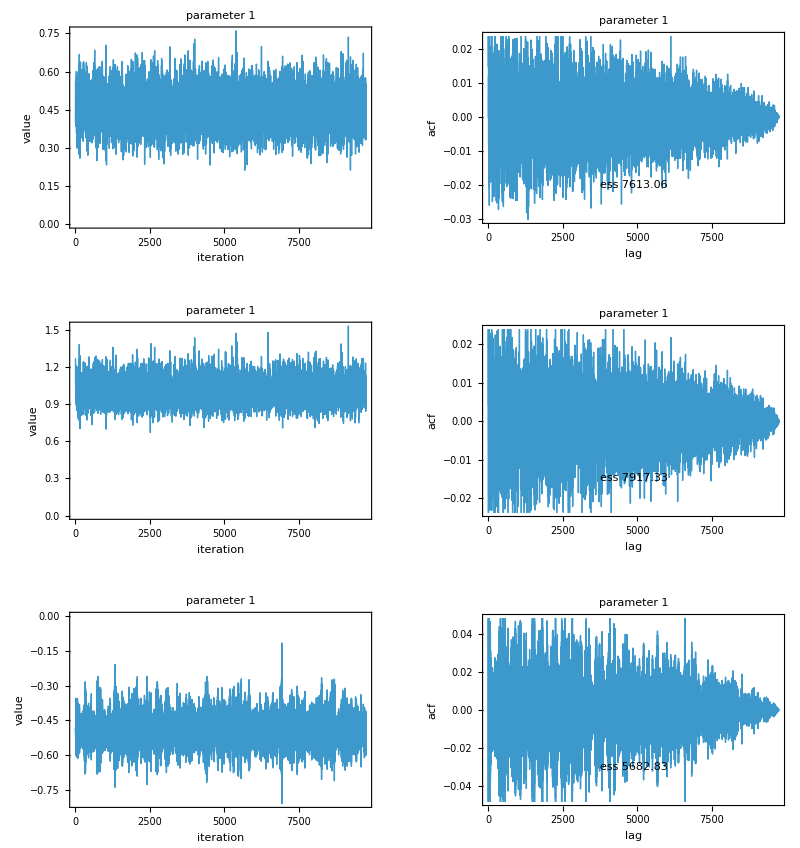

```mathematica
GraphicsGrid[
{
{ListPlot[chain[[1]] , Joined->True , PlotStyle->Thin , Axes->False , Frame->True , FrameLabel->{"iteration" , "value"} , PlotLabel->"parameter 1"] , ListPlot[esses[[1 , 2]] , Joined->True , PlotStyle->Thin , Axes->False , Frame->True , FrameLabel->{"lag" , "acf"} , PlotLabel->"parameter 1",Epilog->Inset[Style["ess "<>ToString[esses[[1 , 1]]]],Scaled[{0.5 , 0.2}]]]},
{ListPlot[chain[[2]] , Joined->True , PlotStyle->Thin , Axes->False , Frame->True , FrameLabel->{"iteration" , "value"} , PlotLabel->"parameter 1"] , ListPlot[esses[[2 , 2]] , Joined->True , PlotStyle->Thin , Axes->False , Frame->True , FrameLabel->{"lag" , "acf"} , PlotLabel->"parameter 1",Epilog->Inset[Style["ess "<>ToString[esses[[2 , 1]]]],Scaled[{0.5 , 0.2}]]]},
{ListPlot[chain[[3]] , Joined->True , PlotStyle->Thin , Axes->False , Frame->True , FrameLabel->{"iteration" , "value"} , PlotLabel->"parameter 1"] , ListPlot[esses[[3 , 2]] , Joined->True , PlotStyle->Thin , Axes->False , Frame->True , FrameLabel->{"lag" , "acf"} , PlotLabel->"parameter 1",Epilog->Inset[Style["ess "<>ToString[esses[[3 , 1]]]],Scaled[{0.5 , 0.2}]]]}
}
]
```

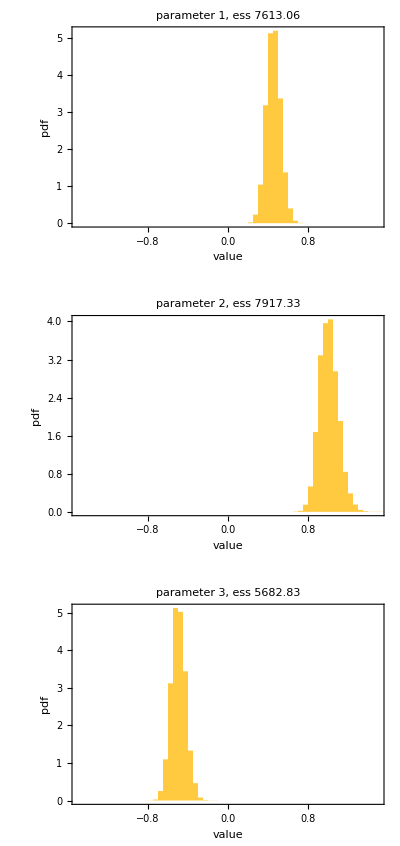

```mathematica
GraphicsColumn[{
Histogram[chain[[1]] , Automatic , "PDF" , ChartStyle->EdgeForm[None] , Axes->False , Frame->True , FrameLabel->{"value" , "pdf"} , PlotRange->{{-1.5 , 1.5} , All} ,PlotLabel->"parameter 1, ess "<>ToString[esses[[1 , 1]]]],
Histogram[chain[[2]] , Automatic , "PDF" , ChartStyle->EdgeForm[None] , Axes->False , Frame->True , FrameLabel->{"value" , "pdf"} , PlotRange->{{-1.5 , 1.5} , All} ,PlotLabel->"parameter 2, ess "<>ToString[esses[[2 , 1]]]],
Histogram[chain[[3]] , Automatic , "PDF" , ChartStyle->EdgeForm[None] , Axes->False , Frame->True , FrameLabel->{"value" , "pdf"} , PlotRange->{{-1.5 , 1.5} , All} ,PlotLabel->"parameter 3, ess "<>ToString[esses[[3 , 1]]]]
}]
```